```mathematica
a=1
```

1

```mathematica
ϕ=1/(2π D)E^(a y)BesselK[0,a r]
```

(ⅇ^y BesselK[0,r])/(2 D π)

```mathematica
ysol=y/.First@Solve[ϕ==d/(2 π D),y]/.C[1]->0
```

Log[d/BesselK[0,r]]

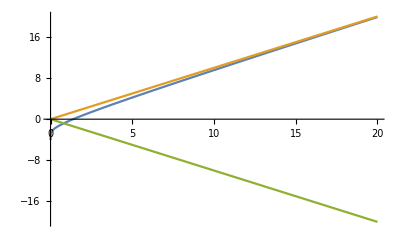

```mathematica
Plot[{ysol/.{d->.25},r,-r},{r,0,20}]
```

```mathematica
ymin[c_]:=r/.FindRoot[E^-r BesselK[0,r]==c,{r,.1}]
ymax[c_]:=r/.FindRoot[E^r BesselK[0,r]==c,{r,.1}]
```

```mathematica
.1//{ymin,ymax}//Through
```

{1.18246,156.83}

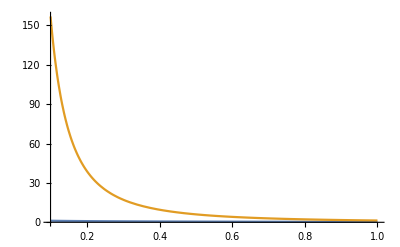

```mathematica
Plot[{ymin[c],ymax[c]},{c,0.1,1},PlotRange->All]
```